```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** PBC is α = 0, OBC is α = 1 **)
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP,σ2])+KroneckerProduct[m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,m0]
```

```mathematica
m0=1.8
```

1.8

```mathematica
(** Bott Index works for both PBC and OBC **)
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,m0,0.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

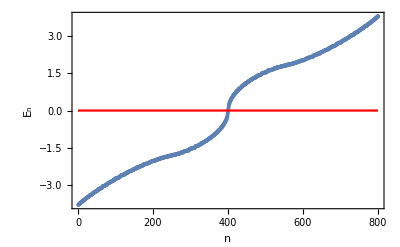

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------- Computation of Bott Index -----------------*)
```

```mathematica
Clear[vecNormalized,ValVecNor,V,U,Ux,Vy,XList, YList, XListKron, YListKron,LogEigenValuesBott,Bott, BottIndex,P]
```

```mathematica
vecNormalized=Table[Normalize[vec[[i]]],{i,1,2 A}];
```

```mathematica
ValVecNor=SortBy[Transpose[{val,vecNormalized}],First];
```

```mathematica
ValVecNor[[1]][[2]];
```

```mathematica
XList = Flatten[Transpose[Table[i,{i,1,Lx},{j,1,Ly}]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
YList = Flatten[Table[i,{i,1,Lx},{j,1,Ly}]];
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
FilledEigenvectors = Table[ValVecNor[[i]][[2]],{i,1,A}];
```

```mathematica
P=Table[0,{i,1,2A},{j,1,2A}];
```

```mathematica
Dimensions[P]
```

{800,800}

```mathematica
Dimensions[TensorProduct[FilledEigenvectors[[1]] ,Conjugate[ FilledEigenvectors[[1]]]]]
```

{800,800}

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i,1,A}]
```

```mathematica
U = P . Ux. P + IdentityMatrix[2 A] - P;
```

```mathematica
V = P . Vy . P + IdentityMatrix[2A] - P;
```

```mathematica
Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];
```

```mathematica
LogEigenValuesBott=Log[Eigenvalues[Bott]];
```

```mathematica
BottIndex = Re[(I/(2π))Total[LogEigenValuesBott]];
```

```mathematica
{m0,BottIndex}
```

{1.8,-1.}